{c→17.5106,k→0.230706,b→17.4842}

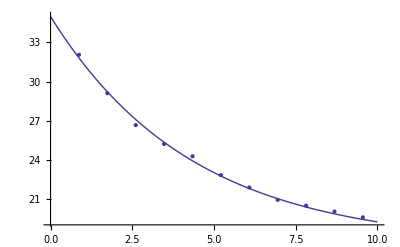

```mathematica
data = {
{0.8685714286,32.0524114286},
{1.7371428572,29.1048228572},
{2.6057142858,26.6572342858},
{3.4742857144,25.2096457144},
{4.342857143,24.2620571429},
{5.2114285716,22.8144685715},
{6.0800000002,21.8668800001},
{6.9485714288,20.9192914287},
{7.8171428574,20.4717028573},
{8.685714286,20.0241142859},
{9.5542857146,19.5765257145},
{10.4228571432,18.6463588573}
};
model = c*Exp[-k*x]+b;
fit = FindFit[data,model,{c,k,b},x,MaxIterations->100000]
ffit = model/. fit;
plot = Plot[ffit, {x,0,10}];
pdata = ListPlot[data];
Show[plot,pdata]
```